```mathematica
e=1;
a=100*^-6;
b=1000*^-6;
l=7*^-3;
L=100*^-3;
θ=15 Degree;
μ=0.12;
W=10*^6;
ϕ0=50;
ϵ=1*^-9;
```

```mathematica
d=Sqrt[a^2 Cos[θ]^2+b^2 Sin[θ]^2];
func=(e ϕ0)/W(a b √π)/d^2 Exp[-xvar^2/a^2-yvar^2/d^2];
αx=func xvar/a^2 d;
αy=func yvar/d;
Intens[x0_,y0_]:=1-(func l d)/a^2((1-(2 xvar^2)/a^2)+a^2/d^2(1-(2 yvar^2)/d^2))/.{xvar->x0,yvar->y0}
x[x0_,y0_]:=L(xvar/l+αx)/.{xvar->x0,yvar->y0}
y[x0_,y0_]:=L(yvar/l+αy)/.{xvar->x0,yvar->y0}
```

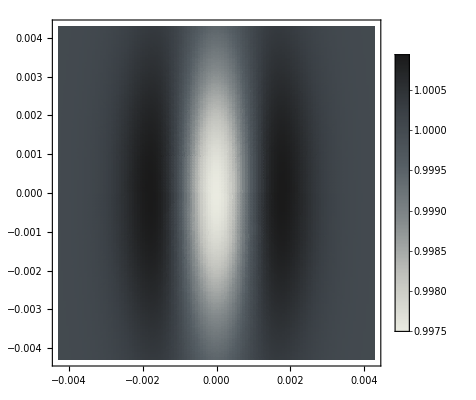

```mathematica
data=Flatten[Table[{x[i,j],y[i,j],Intens[i,j]},{i,-300*^-6,300*^-6,5.*^-6},{j,-300*^-6,300*^-6,5.*^-6}],1];
ListDensityPlot[data,ColorFunction->ColorData[{"GrayTones","Reverse"}],PlotLegends->Automatic]
```